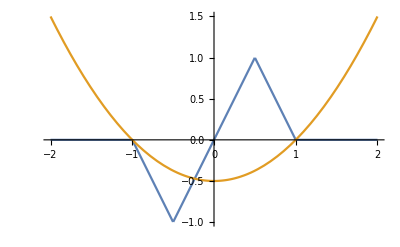

```mathematica
(* Delete everything to prevent accidental variable contamination *)
Remove["Global`*"]
f[x_]:= Piecewise[{{2x, -1/2<x<1/2}, {2(1-x), 1/2<x<1}, {-2(1+x), -1<x<-1/2}}]
G[x_]:=1/2 x^2-1/2
Plot[{f[x],G[x]}, {x, -2, 2}]
```

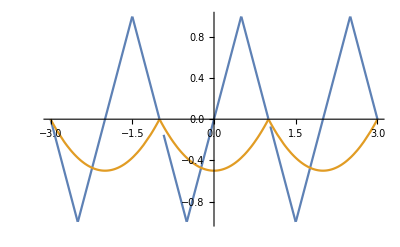

```mathematica
OddExt[x_]:= x - 2Floor[(x+1)/2]
PeriodicF[x_]:=f[OddExt[x]]
PeriodicG[x_]:=G[OddExt[x]]
Plot[{PeriodicF[x], PeriodicG[x]}, {x,-3,3}]
```